```mathematica
(* Riemannian three attractor model {0,1,Infinity} on Pioncare disk with Cauchy wave function: long tailed distribution*)
```

```mathematica
(*Cauchy wave function*)
```

```mathematica
Clear[Ψ,Ψ0,r]
```

```mathematica
Ψ[r_]=Ψ0/(1+r^2)
```

Ψ0/(1+r^2)

```mathematica
(*Normalization*)
```

```mathematica
w=Integrate[Ψ[r],{r,0,Infinity}]
```

(π Ψ0)/2

```mathematica
Ψ0=2/Pi
```

2/π

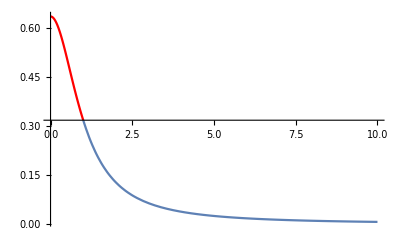

```mathematica
g0=Show[{Plot[Ψ[r],{r,0,1},PlotStyle->Red,PlotRange->All],Plot[Ψ[r],{r,1,10},PlotRange->All]},PlotRange->All]
```

```mathematica
Integrate[Ψ[r],{r,0,r0}]+Integrate[Ψ[r],{r,r0,Infinity}]
```

ConditionalExpression[1, -1<Im[r0]<0||0<Im[r0]<1||Re[r0]≠0]

```mathematica
(*https://en.wikipedia.org/wiki/Schr%C3%B6dinger_equation*)
```

```mathematica
(*Gravitaional Potental*)
```

```mathematica
V=4*Pi*G*m^2/r
```

(4 G m^2 π)/r

```mathematica
E0=(-hbar^2/(2*m))*D[Ψ[r],{r,2}]+V*Ψ[r]-i*hbar*Exp[I*2*m*c^2/hbar]*Ψ[r]
```

-(2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i)/(π (1+r^2))+(8 G m^2)/(r (1+r^2))-(hbar^2 ((8 r^2)/((1+r^2)^3)-2/((1+r^2)^2)))/(m π)

```mathematica
Reduce[E0==0,{m,r}]
```

(hbar i m≠0&&r≠0&&(r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,1]||r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,2]||r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,3]||r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,4]||r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,5]))||(m r (1+r^2)≠0&&G==0&&hbar==0)||(G≠0&&m≠0&&1+r^2≠0&&i==0&&(r==Root[4 G m^3 π+hbar^2 #1+8 G m^3 π #1^2-3 hbar^2 #1^3+4 G m^3 π #1^4&,1]||r==Root[4 G m^3 π+hbar^2 #1+8 G m^3 π #1^2-3 hbar^2 #1^3+4 G m^3 π #1^4&,2]||r==Root[4 G m^3 π+hbar^2 #1+8 G m^3 π #1^2-3 hbar^2 #1^3+4 G m^3 π #1^4&,3]||r==Root[4 G m^3 π+hbar^2 #1+8 G m^3 π #1^2-3 hbar^2 #1^3+4 G m^3 π #1^4&,4]))||(hbar≠0&&m≠0&&G==0&&i==0&&(r==-1/(√3)||r==1/(√3)))

```mathematica
s1=r/.Solve[E0==0,{m,r}]
```

```mathematica
{Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,1],Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,2],Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,3],Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,4],Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,5]}/.m->1.5*10^56
```

Root::deg: 5.47363×10^110 m^3+(7.25979×10^62-6.88411×10^89 ⅇ^((0.+1.70449×10^48 ⅈ) m) i m) #1+1.09473×10^111 m^3 #1^2+(-2.17794×10^63-1.37682×10^90 ⅇ^((«1») m) i m) #1^3+5.47363×10^110 m^3 #1^4-6.88411×10^89 ⅇ^((0.+1.70449×10^48 ⅈ) m) i m #1^5 has fewer than 5 root(s) as a polynomial in #1.

```mathematica
{Root[1.8473504175453281*^279+(7.259792662674554*^62-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i) #1+3.6947008350906563*^279 #1^2+(-2.177937798802366*^63-(1.4378977657328463*^146+1.4824424305008922*^146 ⅈ) i) #1^3+1.8473504175453281*^279 #1^4-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i #1^5&,1],Root[1.8473504175453281*^279+(7.259792662674554*^62-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i) #1+3.6947008350906563*^279 #1^2+(-2.177937798802366*^63-(1.4378977657328463*^146+1.4824424305008922*^146 ⅈ) i) #1^3+1.8473504175453281*^279 #1^4-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i #1^5&,2],Root[1.8473504175453281*^279+(7.259792662674554*^62-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i) #1+3.6947008350906563*^279 #1^2+(-2.177937798802366*^63-(1.4378977657328463*^146+1.4824424305008922*^146 ⅈ) i) #1^3+1.8473504175453281*^279 #1^4-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i #1^5&,3],Root[1.8473504175453281*^279+(7.259792662674554*^62-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i) #1+3.6947008350906563*^279 #1^2+(-2.177937798802366*^63-(1.4378977657328463*^146+1.4824424305008922*^146 ⅈ) i) #1^3+1.8473504175453281*^279 #1^4-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i #1^5&,4],Root[1.8473504175453284*^279+(7.259792662674554*^62-(7.189488828664232*^145+7.41221215250446*^145 ⅈ) i) #1+3.694700835090657*^279 #1^2+(-2.177937798802366*^63-(1.4378977657328463*^146+1.482442430500892*^146 ⅈ) i) #1^3+1.8473504175453284*^279 #1^4-(7.189488828664232*^145+7.41221215250446*^145 ⅈ) i #1^5&,5]}/.#1->6.734680077277472*^27
```

Root::deg: 3.80029370924694×10^390+3.05458×10^83 (-2.17794×10^63-(1.4379×10^146+1.48244×10^146 ⅈ) i)+6.73468×10^27 (7.25979×10^62-(7.18949×10^145+«23» ⅈ) i)-(9.96054×10^284+1.02691×10^285 ⅈ) i has fewer than 1 root(s) as a polynomial in #1.

Root::deg: 3.80029370924694×10^390+3.05458×10^83 (-2.17794×10^63-(1.4379×10^146+1.48244×10^146 ⅈ) i)+6.73468×10^27 (7.25979×10^62-(7.18949×10^145+«23» ⅈ) i)-(9.96054×10^284+1.02691×10^285 ⅈ) i has fewer than 2 root(s) as a polynomial in #1.

Root::deg: 3.80029370924694×10^390+3.05458×10^83 (-2.17794×10^63-(1.4379×10^146+1.48244×10^146 ⅈ) i)+6.73468×10^27 (7.25979×10^62-(7.18949×10^145+«23» ⅈ) i)-(9.96054×10^284+1.02691×10^285 ⅈ) i has fewer than 3 root(s) as a polynomial in #1.

General::stop: Further output of Root::deg will be suppressed during this calculation.

```mathematica
ComplexExpand[1.8473504175453281*^279+(7.259792662674554*^62-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i) 6.734680077277472*^27+3.6947008350906563*^279 (6.734680077277472*^27)^2+(-2.177937798802366*^63-(1.4378977657328463*^146+1.4824424305008922*^146 ⅈ) i) (6.734680077277472*^27)^3+1.8473504175453281*^279 (6.734680077277472*^27)^4-(7.189488828664232*^145+7.412212152504461*^145 ⅈ) i 6.734680077277472*^27]
```

```mathematica
Abs[3.8002937092469362495144323506597561419024513`15.954589770191005*^390+4.528232804868921*^229 -4.392167748894774*^229 i]
```

```mathematica
Sqrt[(3.8002937092469362495144323506597561419024513`15.954589770191005*^390)^2+(4.392167748894774*^229 )^2]
```

```mathematica
(3.8002937092469362495144323506596835422444892`15.954589770191005*^390)^(1/5)
```

1.306060913621316×10^78

```mathematica
Length[%]
```

5

```mathematica
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
```

```mathematica
s2=r/.NSolve[E0==0,r]
```

Root::deg: -1.26328×10^85 m^3+(-1.67552×10^37+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1-2.52657×10^85 m^3 #1^2+(5.02656×10^37+«23» «1» i m) «1»-1.26328×10^85 m^3 #1^4+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m #1^5 has fewer than 5 root(s) as a polynomial in #1.

{Root[-1.26328×10^85 m^3+(-1.67552×10^37+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1-2.52657×10^85 m^3 #1^2+(5.02656×10^37+3.17763×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1^3-1.26328×10^85 m^3 #1^4+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m #1^5&,1],Root[-1.26328×10^85 m^3+(-1.67552×10^37+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1-2.52657×10^85 m^3 #1^2+(5.02656×10^37+3.17763×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1^3-1.26328×10^85 m^3 #1^4+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m #1^5&,2],Root[-1.26328×10^85 m^3+(-1.67552×10^37+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1-2.52657×10^85 m^3 #1^2+(5.02656×10^37+3.17763×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1^3-1.26328×10^85 m^3 #1^4+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m #1^5&,3],Root[-1.26328×10^85 m^3+(-1.67552×10^37+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1-2.52657×10^85 m^3 #1^2+(5.02656×10^37+3.17763×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1^3-1.26328×10^85 m^3 #1^4+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m #1^5&,4],Root[-1.26328×10^85 m^3+(-1.67552×10^37+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1-2.52657×10^85 m^3 #1^2+(5.02656×10^37+3.17763×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m) #1^3-1.26328×10^85 m^3 #1^4+1.58881×10^64 2.71828^((0.+1.70449×10^48 ⅈ) m) i m #1^5&,5]}

```mathematica
Expand[FullSimplify[ExpandAll[(-1.2632839787127338*^85 m^3+(-1.6755203232937521*^37+1.5888144903109397*^64 2.718281828459045^((0.+1.7044917108638446*^48 ⅈ) m) i m) #1-2.5265679574254676*^85 m^3 #1^2+(5.026560969881256*^37+3.1776289806218795*^64 2.718281828459045^((0.+1.7044917108638446*^48 ⅈ) m) i m) #1^3-1.2632839787127338*^85 m^3 #1^4+1.5888144903109397*^64 2.718281828459045^((0.+1.7044917108638446*^48 ⅈ) m) i m #1/.#1->r/.m->1.5*10^56)/(-4.263583428155479*^253)]]
```

```mathematica
ExpandAll[(-4.263583428155479*^253+r (-1.6755203232937521*^37+r (-8.527166856310958*^253+(5.026560969881256*^37-4.263583428155479*^253 r) r)+i ((3.3185891681050953*^120+3.4213958109130896*^120 ⅈ)+(3.3185891681050953*^120+3.4213958109130896*^120 ⅈ) r^2)))/((-4.263583428155479*^253))]
```

```mathematica
NSolve[1.0+3.929840594250127*^-217 r-(7.783568033851728*^-134+8.024695349736035*^-134 ⅈ) i r+2.0* r^2-1.178952178275038*^-216 r^3-(7.783568033851728*^-134+8.024695349736035*^-134 ⅈ) i r^3+ r^4==0,r]
```

{{r→6.7194×10^-290 (4.38637×10^72+(2.89593×10^155+2.98564×10^155 ⅈ) i)-0.5 √(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))-0.5 √(-2.66667-(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-(0.25 (0.+2.15021×10^-288 (-4.38637×10^72-(2.89593×10^155+2.98564×10^155 ⅈ) i)+7.16736×10^-289 (-4.38637×10^72+(8.68779×10^155+8.95693×10^155 ⅈ) i)))/(√(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))))},{r→6.7194×10^-290 (4.38637×10^72+(2.89593×10^155+2.98564×10^155 ⅈ) i)-0.5 √(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))+0.5 √(-2.66667-(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-(0.25 (0.+2.15021×10^-288 (-4.38637×10^72-(2.89593×10^155+2.98564×10^155 ⅈ) i)+7.16736×10^-289 (-4.38637×10^72+(8.68779×10^155+8.95693×10^155 ⅈ) i)))/(√(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))))},{r→6.7194×10^-290 (4.38637×10^72+(2.89593×10^155+2.98564×10^155 ⅈ) i)+0.5 √(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))-0.5 √(-2.66667-(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+(0.25 (0.+2.15021×10^-288 (-4.38637×10^72-(2.89593×10^155+2.98564×10^155 ⅈ) i)+7.16736×10^-289 (-4.38637×10^72+(8.68779×10^155+8.95693×10^155 ⅈ) i)))/(√(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))))},{r→6.7194×10^-290 (4.38637×10^72+(2.89593×10^155+2.98564×10^155 ⅈ) i)+0.5 √(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))+0.5 √(-2.66667-(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+(0.25 (0.+2.15021×10^-288 (-4.38637×10^72-(2.89593×10^155+2.98564×10^155 ⅈ) i)+7.16736×10^-289 (-4.38637×10^72+(8.68779×10^155+8.95693×10^155 ⅈ) i)))/(√(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))))}}

```mathematica
FindRoot[-4.263583428155479*^253+r (-1.6755203232937521*^37+r (-8.527166856310958*^253+(5.026560969881256*^37-4.263583428155479*^253 r) r)+i ((3.3185891681050953*^120+3.4213958109130896*^120 ⅈ)+(3.3185891681050953*^120+3.4213958109130896*^120 ⅈ) r^2))==0,{r,6.734680077277472*^27}]
```

FindRoot::nlnum: The function value {-4.26358×10^253+6.73468×10^27 (-1.30234388522904×10^337+(1.50518×10^176+1.55181×10^176 ⅈ) i)} is not a list of numbers with dimensions {1} at {r} = {6.73468×10^27}.

FindRoot[-4.26358×10^253+r (-1.67552×10^37+r (-8.52717×10^253+(5.02656×10^37-4.26358×10^253 r) r)+i ((3.31859×10^120+3.4214×10^120 ⅈ)+(3.31859×10^120+3.4214×10^120 ⅈ) r^2))==0,{r,6.73468×10^27}]

```mathematica
Abs[r]/.NSolve[1+2. r^2+1. r^4==0,r]
```

{Abs[6.7194×10^-290 (4.38637×10^72+(2.89593×10^155+2.98564×10^155 ⅈ) i)-0.5 √(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))-0.5 √(-2.66667-(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-(0.25 (0.+2.15021×10^-288 (-4.38637×10^72-(2.89593×10^155+2.98564×10^155 ⅈ) i)+7.16736×10^-289 (-4.38637×10^72+(8.68779×10^155+8.95693×10^155 ⅈ) i)))/(√(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))))],Abs[6.7194×10^-290 (4.38637×10^72+(2.89593×10^155+2.98564×10^155 ⅈ) i)-0.5 √(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))+0.5 √(-2.66667-(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-(0.25 (0.+2.15021×10^-288 (-4.38637×10^72-(2.89593×10^155+2.98564×10^155 ⅈ) i)+7.16736×10^-289 (-4.38637×10^72+(8.68779×10^155+8.95693×10^155 ⅈ) i)))/(√(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))))],Abs[6.7194×10^-290 (4.38637×10^72+(2.89593×10^155+2.98564×10^155 ⅈ) i)+0.5 √(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))-0.5 √(-2.66667-(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+(0.25 (0.+2.15021×10^-288 (-4.38637×10^72-(2.89593×10^155+2.98564×10^155 ⅈ) i)+7.16736×10^-289 (-4.38637×10^72+(8.68779×10^155+8.95693×10^155 ⅈ) i)))/(√(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))))],Abs[6.7194×10^-290 (4.38637×10^72+(2.89593×10^155+2.98564×10^155 ⅈ) i)+0.5 √(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))+0.5 √(-2.66667-(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)-2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+(0.25 (0.+2.15021×10^-288 (-4.38637×10^72-(2.89593×10^155+2.98564×10^155 ⅈ) i)+7.16736×10^-289 (-4.38637×10^72+(8.68779×10^155+8.95693×10^155 ⅈ) i)))/(√(-1.33333+(9.3678×10^-276 (6.64446282412769×10^578-(7.62158×10^228+7.85769×10^228 ⅈ) i+(4.7488857671391×10^310-1.55631829665681×10^312 ⅈ) i^2))/(-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3)+2.85614×10^-304 (-1.01736489886712×10^911+(1.75046300482666×10^561+1.80469063463255×10^561 ⅈ) i-(1.0906862938581×10^643-3.574428020126311×10^644 ⅈ) i^2+5.19615 √(-3.99616467726369×10^1388+(7.44872035547824×10^1038+7.67947441817517×10^1038 ⅈ) i-(4.4031725630584×10^1120-1.44302018604954×10^1122 ⅈ) i^2+(1.63991540069558×10^1204-1.49631330337337×10^1204 ⅈ) i^3+(1.57588144508×10^1287+9.6261225924295×10^1285 ⅈ) i^4-(6.77515134659426×10^937+7.89616443647398×10^937 ⅈ) i^5+(4.5080126166854×10^1019-4.91236458683258×10^1020 ⅈ) i^6))^(1/3))))]}

```mathematica
((4 c^6 G m^3 π)/hbar^2/.m->1.5*10^56)^(1/5)
```

7.13362×10^55

```mathematica
((4 c^6 G m^3 π)/hbar^2)^(1/5)
```

```mathematica
m/.NSolve[1.4049313422810796*^22 (m^3)^(1/5)-6.734680077277472*^27==0,m]
```

{{m→2.93609×10^9},{m→-1.46805×10^9-2.54273×10^9 ⅈ},{m→-1.46805×10^9+2.54273×10^9 ⅈ}}

```mathematica
2*Pi*hbar/(m*c)/.NSolve[1.4049313422810796*^22 (m^3)^(1/5)-6.734680077277472*^27==0,m]
```

{7.52776×10^-47,-3.76388×10^-47+6.51923×10^-47 ⅈ,-3.76388×10^-47-6.51923×10^-47 ⅈ}

```mathematica
2*G*m/c^2/.NSolve[1.4049313422810796*^22 (m^3)^(1/5)-6.734680077277472*^27==0,m]
```

{4.35966×10^-19,-2.17983×10^-19-3.77558×10^-19 ⅈ,-2.17983×10^-19+3.77558×10^-19 ⅈ}

```mathematica
Sqrt[6.734680077277472*^27*7.527762213556405*^-47]/e
```

1.48238

```mathematica
m/.NSolve[1.4049313422810796*^22 (m^3)^(1/5)-7.133618117302776*^55==0,m]
```

{-7.5×10^55-1.29904×10^56 ⅈ,-7.5×10^55+1.29904×10^56 ⅈ,1.5×10^56}

```mathematica
2*Pi*hbar/(m*c)/.NSolve[1.4049313422810796*^22 (m^3)^(1/5)-7.133618117302776*^55==0,m]
```

{-7.3674×10^-94+1.27607×10^-93 ⅈ,-7.3674×10^-94-1.27607×10^-93 ⅈ,1.47348×10^-93}

```mathematica
Sqrt[6.734680077277472*^27*1.4734805731648847*^-93]
```

3.15015×10^-33

```mathematica
2*G*m/c^2/.NSolve[1.4049313422810796*^22 (m^3)^(1/5)-7.133618117302776*^55==0,m]
```

{-1.11364×10^28-1.92888×10^28 ⅈ,-1.11364×10^28+1.92888×10^28 ⅈ,2.22728×10^28}

```mathematica
(4.35966191095696*^-19*2.2272772912568603*^28*7.527762213556405*^-47*1.4734805731648847*^-93*7.133618117302776*^55)^(1/5)
```

2.38292×10^-15

```mathematica
2*Pi*hbar/(2.382919947161434*^-15*c)
```

9.27526×10^-23

```mathematica
(2.8900127725052614*^48)/r^2/2/.r->8.8*10^28/2
```

7.46388×10^-10

```mathematica
m/.Solve[%-2*m*c^2/(4*Pi*(8.8*10^28/2)^3/3)==0,m]
```

{1.48163×10^56}

```mathematica
%/(1.5*10^56)
```

{0.987753}